Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1.  Let f[x, y] = k when 8 ≤ x ≤ 12 and 0 ≤ y ≤ 2 and zero elsewhere. Find k. Find P(X ≤ 11, 1 ≤ Y ≤1.5) and P(9 ≤ X ≤ 13, Y ≤ 1).

I can define a rectangle as a region. This will be a continuous function.

```mathematica
d1=Rectangle[{8,0},{12,2}];
```

And test it.

```mathematica
RegionMember[d1,{x,y}]
```

(x|y)∈Reals&&8≤x≤12&&0≤y≤2

I can define f[x, y] as a piecewise function

```mathematica
f[x_,y_]=Piecewise[{{k, {x,y}∈d1},{0,{x,y}∉d1}}]
```

Piecewise[{{k, {x,y}∈Rectangle[{8,0},{12,2}]}, {0, True}}]

Checking the area.

```mathematica
4 2
```

8

Knowing the area of the rectangle, I can update the function definition

```mathematica
f[x_,y_]=Piecewise[{{0.125, {x,y}∈d1},{0,{x,y}∉d1}}]
```

Piecewise[{{0.125, {x,y}∈Rectangle[{8,0},{12,2}]}, {0, True}}]

Having the PDF, I should be able to come up with some automation from Mathematica, but I haven’t found it yet. For this particular problem, it is a simple operation, and I just do the simple calculations. For X ≤ 11, 1 ≤ Y ≤1.5) I can find the probability of the volume

```mathematica
3 0.5 0.125
```

0.1875

And for 9 ≤ X ≤ 13, Y ≤ 1 there is peculiarity, because x = 0 when beyond 12. So that side is only 3 units wide.

```mathematica
3 1 0.125
```

0.375

The green cells above match the answer in the text.

3.  Let f[x, y] = k if x > 0, y > 0, x + y < 3 and 0 otherwise. Find k. Sketch f[x, y]. Find P(X + Y ≤ 1), P(Y > X).

```mathematica
Clear["Global`*"]
```

This is similar to the last problem.

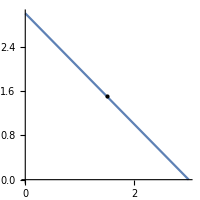

```mathematica
Plot[3-x, {x,0,3},AspectRatio->Automatic,ImageSize->200, Epilog->{Point[{1.5,1.5}]}]
```

I can make a 2D domain of a graphic region.

```mathematica
d2=Polygon[{{0,0},{3,0},{0,3},{0,0}}]
```

Polygon[{{0,0},{3,0},{0,3},{0,0}}]

I can test the region to make sure it is recognized.

```mathematica
RegionMember[d2,{x,y}]
```

(x|y)∈Reals&&3 y≥0&&-3 (-3+x)-3 y≥0&&3 x≥0

I can define a function using the interior of the region as domain. This is another continuous function with a constant function value.

```mathematica
f[x_,y_]=Piecewise[{{k, {x,y}∈d2},{0,{x,y}∉d2}}]
```

Piecewise[{{k, {x,y}∈Polygon[{{0,0},{3,0},{0,3},{0,0}}]}, {0, True}}]

The area of the region is

```mathematica
Area[d2]
```

9/2

allowing me to update the function with the simple volume.

```mathematica
f[x_,y_]=Piecewise[{{2/9, {x,y}∈d2},{0,{x,y}∉d2}}]
```

Piecewise[{{2/9, {x,y}∈Polygon[{{0,0},{3,0},{0,3},{0,0}}]}, {0, True}}]

As for the first probability, it is a simple volume calculation, as in the last problem: P (X + Y <= 1)

```mathematica
1/2* 2/9
```

1/9

The second probabilty focuses on a triangle P (Y > X). The point in the plot above suggests the symmetry which simplifies the volume calculation.

```mathematica
1.5 1.5 2/9
```

0.5

The green cells above match the answer in the text.

5.  Find the density of the marginal distribution of Y in figure 524.

Referring to example 2 and figure 524 on p. 1053, I see that α_1 and β_1 are on the x-axis, and the other two on the y-axis.

This is a continuous uniform distribution. Numbered line (8) in the example explains that

(β_1-α_1)*(β_2-α_2)=k

and that

f[x, y]=1/k

Numbered line (16) on p. 1055 concerns finding the marginal distribution of Y, the topic of this problem, and states that

f_2[y]=∫_(-∞)^∞ f[x,y]ⅆx

The above can be transformed into

∫_α_1^β_1 1/((β_1-α_1)*(β_2-α_2))ⅆx

the limits of integration changed from their improper integral values because I can only integrate within the domain of f[x, y]. Since the integrand is a constant, the result of the integration is

(β_1-α_1)/((β_1-α_1)*(β_2-α_2))=1/(β_2-α_2)

and this result agrees with the answer in the text.

7.  What are the mean thickness and the standard deviation of transformer cores each consisting of 50 layers of sheet metal and 49 insulating paper layers if the metal sheets have mean thickness 0.5 mm each with a standard deviation of 0.05 mm and the paper layers have mean 0.05 mm each with a standard deviation of 0.02 mm?

I do not have a plan to solve this. It seems like it will not be possible to get an exact answer. But I have made two groups using the input from the problem description.

```mathematica
datam=RandomVariate[NormalDistribution[0.5,0.05],50]
```

{0.558216,0.566597,0.538682,0.4675,0.541684,0.550354,0.489031,0.478492,0.487061,0.467497,0.519695,0.396914,0.521427,0.511171,0.444294,0.455204,0.499849,0.504318,0.516317,0.457775,0.408534,0.577282,0.501376,0.468424,0.409549,0.506527,0.372988,0.522404,0.508176,0.543568,0.529384,0.499485,0.512613,0.452279,0.530811,0.529966,0.503148,0.484531,0.45554,0.503649,0.607374,0.485367,0.436549,0.519838,0.430133,0.534794,0.530962,0.479134,0.510001,0.546354}

```mathematica
part1=Total[datam]
```

24.8728

```mathematica
m1=Mean[datam]
```

0.497456

```mathematica
StandardDeviation[datam]
```

0.0474566

```mathematica
datap=RandomVariate[NormalDistribution[0.05,0.02],49]
```

{0.0395329,0.0466633,0.0180818,0.0265622,0.0500569,0.0452602,0.0393113,0.0664617,0.0619587,0.0417175,0.0361719,0.0615357,0.0458454,0.0463132,0.0329824,0.0627634,0.0528396,0.0712693,0.0676439,0.0457183,0.050865,0.0251026,0.0664769,0.0719348,0.0415759,0.0675027,0.0726362,0.0549021,0.0472956,0.0485101,0.0372773,0.075856,0.0752395,0.0575842,0.0612874,0.0539422,0.0684779,0.0620852,0.036947,0.0510526,0.0452759,0.0371434,0.0541386,0.0681146,0.0659026,0.0525161,0.0734824,0.0470252,0.0331304}

```mathematica
part2=Total[datap]
```

2.56197

```mathematica
m2=Mean[datap]
```

0.0522851

```mathematica
StandardDeviation[datap]
```

0.0143689

```mathematica
part1+part2
```

27.4348

Above in yellow I added the two sets of randomly generated data. As the text answer is 27.45, I think it is not a bad result. The text answer for standard deviation is 0.38 mm. This is so large I don’t know what to do with it. The text theorem 3, p. 1058, discusses ways to get standard deviations for multivariate distributions from variances, and if I was really interested in getting the text answer I would pursue this.

```mathematica
proposeddeviation=(50(0.04745)+49 (0.01436))/99
```

0.0310721

11.  A 5-gear assembly is put together with spacers between the gears. The mean thickness of the gears is 5.020 cm with a standard deviation of 0.003 cm. The mean thickness of the spacers is 0.040 cm with a standard deviation of 0.002 cm. Find the mean and standard deviation of the assembled units consisting of 5 randomly selected gears and 4 randomly selected spacers.

This problem should be done in some multivariate form, else the spirit of the section is being ignored. But I go on anyway with

```mathematica
Clear["Global`*"]
```

I mix up a batch of gears using the specification.

```mathematica
datag=RandomVariate[NormalDistribution[5.020,0.003],5]
```

{5.01884,5.01166,5.02166,5.02156,5.01753}

and add up the total thickness of the virtual gears

```mathematica
part1=Total[datag]
```

25.0913

and calculate the mean (though it won’t be used).

```mathematica
m1=Mean[datag]
```

5.01825

The standard deviation has increased slightly from the original, which seems reasonable.

```mathematica
sd1=StandardDeviation[datag]
```

0.00408888

Now I make a set of spacers, using their spec

```mathematica
datas=RandomVariate[NormalDistribution[0.040,0.002],4]
```

{0.0373853,0.0412382,0.0409712,0.0430944}

and add up the total thickness.

```mathematica
part2=Total[datas]
```

0.162689

And check the mean (again, not to be used).

```mathematica
m2=Mean[datas]
```

0.0406723

Again the standard deviation has increased slightly from the original.

```mathematica
sd2=StandardDeviation[datas]
```

0.00238609

Adding up the assembly thickness, I see it is pretty close to the text answer, which is 25.26.

```mathematica
totg=part1+part2
```

25.2539

The combination of standard deviations follows from something I found on some site, but it is less than half the standard deviation shown in the text answer (0.0078 cm).

```mathematica
(5 sd1+4 sd2)/9
```

0.00333209

Again I take the opportunity to shine on the text method of calculating bivariate standard deviations.

13.  Find P(X > Y) when (X, Y) has the density f[x, y] = 0.25 ⅇ^(-0.5(x+y)) if x ≥ 0, y ≥ 0 and 0 otherwise.

```mathematica
Clear["Global`*"]
```

I can plot the pdf in a contour plot.

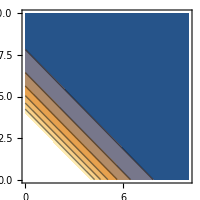

```mathematica
ContourPlot[0.25 ⅇ^(-0.5(x+y)),{x,0,10}, {y,0,10},ImageSize->200]
```

I can check to see where the pdf is normalized.

```mathematica
Table[Integrate[0.25 ⅇ^(-0.5(x+y)),{x,0,k},{y,0,k}],{k,30,40}]
```

{0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

I can express the domain of the bivariate pdf as a region.

```mathematica
d2=Region[x≥0&&y≥0,{x,y}]
```

Region[x≥0&&y≥0,{x,y}]

I can define the pdf in terms of the domain region.

```mathematica
f[x_,y_]=Piecewise[{{0.25 ⅇ^(-0.5(x+y)),x≥0&&y≥0},{0,x<0&&y<0}}]
```

Piecewise[{{0.25 ⅇ^(-0.5 (x+y)), x≥0&&y≥0}, {0, True}}]

I plot the pdf to see that Mathematica is responding to the function definition.

```mathematica
Plot3D[f[x,y],{x,30,40},{y,30,40}]
```

-Graphics3D-

I try to roll a custom distribution to incorporate the pdf, but it doesn’t seem functional.

```mathematica
d1=ProbabilityDistribution[f[{x,y}],{x,0,1},{y,0,1}]
```

ProbabilityDistribution[f[{x1,x2}],{x1,0,1},{x2,0,1}]

I try a different standard distribution, particularized to the area where the pdf has shown consistency.

```mathematica
d2=BinormalDistribution[{35,35},{0.001,0.001},0]
```

BinormalDistribution[{35,35},{0.001,0.001},0]

As shown in the plot below, this distribution has a pdf with no character. The comparison of particular input values must be left to the mean and stand. dev. within the distribution.

```mathematica
Plot3D[Evaluate[PDF[d2,{x,y}]],{x,0,40},{y,0,40},Exclusions->None,PlotRange-> All]
```

-Graphics3D-

I request the diagnostic probability.

```mathematica
Probability[x-y>0,{x,y}\[Distributed]d2]
```

0.5

I don’t really know if I showed anything or not, but the green cell matches the answer in the text.

```mathematica
lisdis=Table[BinormalDistribution[{n,n},{0.001,0.001},0],{n,35,99}];
Length[lisdis]
```

65

I wanted to take a longer view but the following input line would not process.

```mathematica
Table[Probability[x-y>0,{x,y}\[Distributed]lisdis[[n]]],{n,1,65}]
```

$Aborted

15.  Give an example of two different discrete distributions that have the same marginal distributions.

17.  Let (X, Y) have the probability function f[0, 0] = f[1, 1] = 1/8, f[0, 1] = f[1, 0] = 3/8. Are X and Y independent?

No they are not independent. All the possible occurrences in the distribution are taken up at the four points listed. The points being locked, the coordinates making up the points are likewise locked.